#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy]
Off[LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={0.5(*,1.5*)};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.8)^(-8);
```

```mathematica
ClearAll;
ImgSize=900;
hbarc=197.32858;
mn=938.3;
Subscript[α, fine]=1./137.;
hat[l_]:=Sqrt[2 l+1];
resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v18g4/results";
tmpDir="/home/kirscher/kette_repo/ComptonLIT/systems/tmp";
SetDirectory[resultsDir]
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"]
```

/home/kirscher/kette_repo/ComptonLIT/systems/mul_helion_miwchan-v18g4/results

Import::nffil: File dtype.dat not found during Import.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

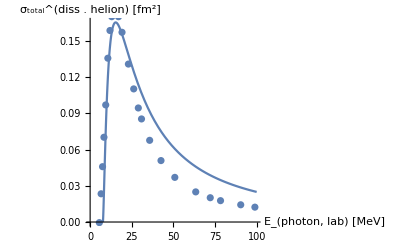

```mathematica
He3DatamBarnGolak=Import["../../../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../../../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{es=Re[Eigensystem[norm]],ovsqi,ovsq,n},Print["min/max: ",MinMax[es[[1]]]];n=Length[Select[es[[1]],#<cutoff&]];Print["(min/max) discarded elements: ",n," ",MinMax[Select[es[[1]],#<cutoff&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@es[[1]]];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@es[[1]]];
{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}]

normreg[noMa_,threshold_]:=Block[
{es=Eigensystem[noMa],μ,transf},
{μ,transf}=Transpose[Select[Transpose[es],Re[#[[1]]]>threshold&]];
{(Transpose[transf].DiagonalMatrix[μ^(-1/2)])}];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}];
```

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

B(^3He) = -6.58729

Dim_full^helion = 672=^!672   ;     Dim_(non - singular)^helion = 653

Dot::dotsh: Tensors {{-5.22283×10^-35,-2.8556×10^-33,-3.95673×10^-31,-2.57477×10^-29,-1.39409×10^-27,-6.8231×10^-26,-2.83261×10^-24,-7.97734×10^-23,-2.23482×10^-31,-5.39043×10^-31,-8.53553×10^-31,-4.39827×10^-28,-3.29267×10^-26,«26»,-4.38646×10^-18,-2.20838×10^-21,-1.1946×10^-20,-6.4204×10^-20,-3.38257×10^-19,-1.67632×10^-18,-6.8965×10^-18,-1.61795×10^-17,-4.7856×10^-18,-4.72078×10^-35,-2.58104×10^-33,«622»},«49»,«603»} and {-1.30435×10^-7,-1.41984×10^-8,-8.73445×10^-9,8.28361×10^-8,1.74612×10^-7,-7.40618×10^-8,1.7164×10^-8,7.19788×10^-9,-7.43443×10^-9,3.79343×10^-8,-2.31601×10^-7,8.53021×10^-9,-2.31715×10^-6,-4.24358×10^-8,«24»,-1.66303×10^-7,5.7642×10^-6,1.04416×10^-7,1.60254×10^-7,-1.94299×10^-6,0.000081897,3.60384×10^-7,7.6439×10^-7,6.70693×10^-7,7.12733×10^-6,-0.0000113569,-0.0000127817,«603»} have incompatible shapes.

ListPlot::lpn: Re[{{-5.22283×10^-35,-2.8556×10^-33,-3.95673×10^-31,-2.57477×10^-29,-1.39409×10^-27,-6.8231×10^-26,-2.83261×10^-24,-7.97734×10^-23,-2.23482×10^-31,-5.39043×10^-31,-8.53553×10^-31,-4.39827×10^-28,«27»,-4.38646×10^-18,-2.20838×10^-21,-1.1946×10^-20,-6.4204×10^-20,-3.38257×10^-19,-1.67632×10^-18,-6.8965×10^-18,-1.61795×10^-17,-4.7856×10^-18,-4.72078×10^-35,-2.58104×10^-33,«622»},{0.,«49»,«622»},«48»,«603»}.{«1»}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

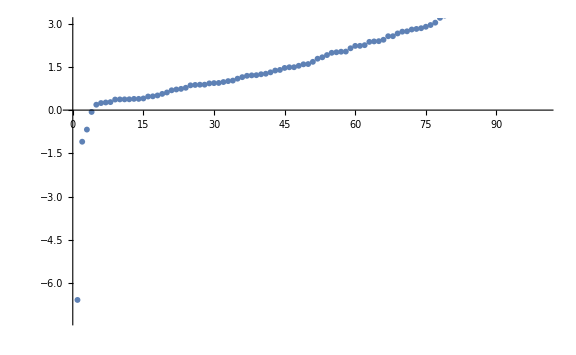
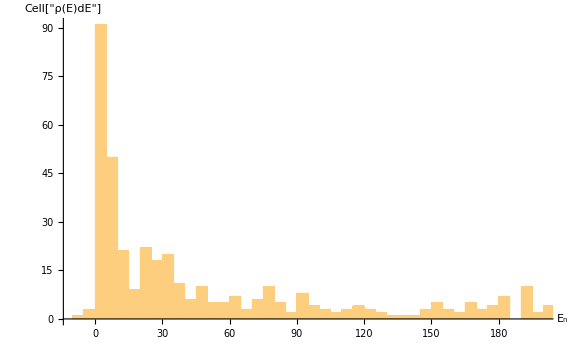
ListPlot[1] | 
-Graphics- | -Graphics-
 |  |  |  |

```mathematica
Oμ=normreg[He3Norm,thresholdLIT][[1]];

orderedEVSYHe3=Sort[Transpose[Eigensystem[{(Transpose[Oμ].He3Ham).Oμ,(Transpose[Oμ].He3Norm).Oμ}]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0=orderedEVSYHe3[[1,1]];v0=orderedEVSYHe3[[1,2]];

dE=5;
Print["B(^3He) = ",e0];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0][[1]]]
fullv0=Transpose[Oμ].v0;
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,AxesLabel->{MaTeX["\\text{Norm-Eigenvector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{1.1 e0,3}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=("./mat_"<>ToString[#]<>"^-")&/@Subscript[I, n];
LitNormHamMat=readREAL8list[#]&/@matnames;

LITbasisDim=IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat;
LitNorm=ArrayReshape[LitNormHamMat[[#]][[1;;LITbasisDim[[#]]^2]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];LitHam=ArrayReshape[LitNormHamMat[[#]][[LITbasisDim[[#]]^2+1;;]],{LITbasisDim[[#]],LITbasisDim[[#]]}]&/@Range[1,Length[Subscript[I, n]]];
Print["N_final = ",LITbasisDim];
```

OpenRead::noopen: Cannot open ./mat_0.5^-.

BinaryRead::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

BinaryReadList::stream: $Failed is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[BinaryReadList[$Failed],{1,1}].

BinaryReadList::noopen: Cannot open Real64.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[$Failed,{1,1}].

N_final = {1}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in Norm-Eigen-Vector Basis

min/max: {-1.16333×10^-7,130.381}

(min/max) discarded elements: 1143 {-1.16333×10^-7,5.39858×10^-9}

J=0.5:  E_0=-2.20765

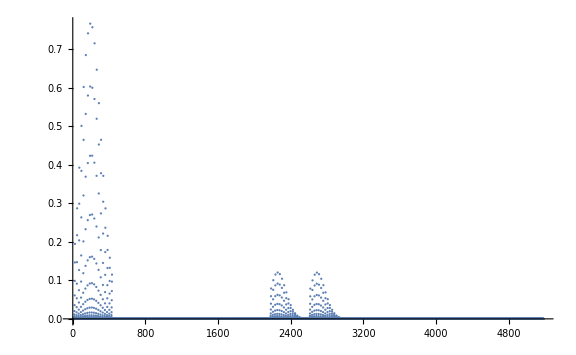
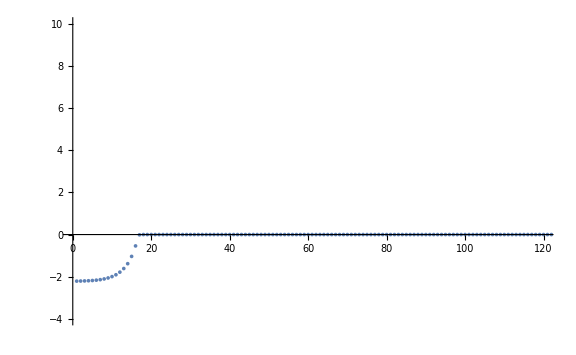
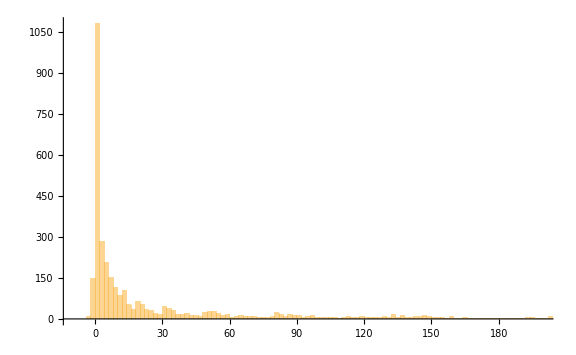
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
LitNmhis={};
LitEigSys={};
fullv0l={};
dE=2.;
Do[
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]],thresholdLIT];
AppendTo[LitNmhis,{LitNmh,LitNmhi}];
orderedEVSYOut=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
e0l=orderedEVSYOut[[1,1]];v0l=orderedEVSYOut[[1,2]];
Print["J=",Subscript[I, n][[nj]],":  E_0=",e0l];
AppendTo[fullv0l,Transpose[LitNmh].v0l];
AppendTo[LitEigSys,orderedEVSYOut];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
Grid[{{
ListPlot[Re[fullv0l],PlotRange->Full,AxesLabel->{MaTeX["\\text{Norm eigenvector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[#[[All,1]]&/@LitEigSys,PlotRange->{{0,120},{-4,10}},AxesLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[#[[All,1]]&/@LitEigSys,{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}]
}}]
```

E_n=-4.88129×10^-14

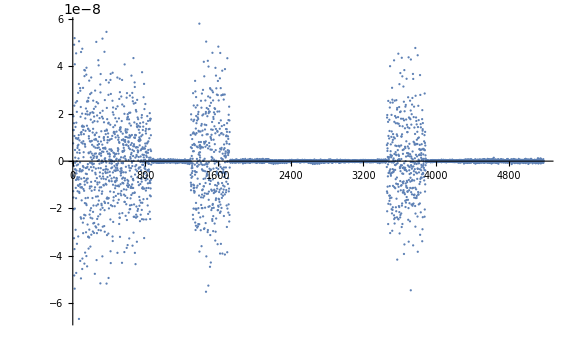

```mathematica
NO=50;
eM=orderedEVSYOut[[NO,1]];vM=orderedEVSYOut[[NO,2]];
Print["E_n=",eM];
fullvM=Transpose[LitNmh].vM;
ListPlot[Re[fullvM],PlotRange->Full,AxesLabel->{MaTeX["\\text{Norm eigenvector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\propto\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

```mathematica
CouplingBlockj={};
Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

nk=Max[ToExpression[StringSplit[FileNames["*_S_"<>JLIT<>"*"],"_"][[All,1]]]];
ks=Range[0,nk];

CouplingBlock={};
CouplingBlockT={};
Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];

tmp =BinaryReadList["InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"."<>dt,"Real32"];
OutDim=Dimensions[tmp][[1]]/He3BasisDim;
test=ArrayReshape[tmp,{OutDim,He3BasisDim}];
AppendTo[CouplingBlockT,{mIn,test}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
(*Clear[CouplingBlock];*)
,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim(⟨ψ|ο̂|helion⟩) = ",Dimensions[CouplingBlockj[[#]][[1]][[2]]&/@Range[1,Length[Subscript[I, n]]]]];
Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Dimensions[LitHam]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Dimensions[LitNorm]];
```

Range::range: Range specification in Range[0,-∞] does not have appropriate bounds.

BinaryReadList::noopen: Cannot open InMIn_0.5_-0.5.$Failed.

Part::partw: Part 1 of {} does not exist.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[$Failed,{({}⟦1⟧)/672,672}].

BinaryReadList::noopen: Cannot open InMIn_0.5_0.5.$Failed.

Part::partw: Part 1 of {} does not exist.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[$Failed,{({}⟦1⟧)/672,672}].

Dim(⟨ψ|ο̂|helion⟩) = {1}

Dim(⟨ψ|Ĥ|ψ⟩) = {1}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {1}

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
{λsHeEB,trfHeEB}=Re[Eigensystem[(Transpose[OμRHSEB].He3Ham).OμRHSEB]];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};

(*{λsHe,trfHe}=Re[Eigensystem[{He3Ham,He3Norm}]];
evgs=Flatten[trfHe[[TakeSmallest[λsHe->"Index",1]]]];
inhomo={};*)

Do[
Do[
tmp=CouplingBlockj[[nj]][[mm]][[2]];

OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]]];
{λfinalEB,trfLitEB}=Re[Eigensystem[(Transpose[OμLHSEB].LitHam[[nj]]).OμLHSEB]];
AppendTo[inhomoEB,Transpose[OμLHSEB].((tmp.OμRHSEB).evgsEB)];

(*{λfinal,trfLit}=Re[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]];
AppendTo[inhomo,tmp.evgs];*)
,{mm,Range[1,Length[mIns[[nj]]]]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

E_0^initial = -6.60029    dim(initial) = {672}

E_0^final  = -2.2077    dim(final)   = {4041}

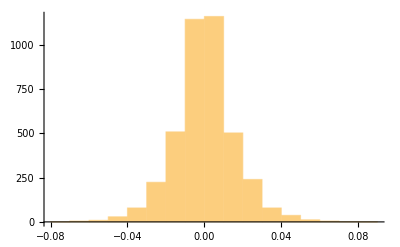

```mathematica
lpsisEV={};CumStrengthsEV={};

esEV=Re[Eigensystem[He3Norm]];
{μEV,transfEV}=Transpose[Select[Transpose[esEV],Re[#[[1]]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Re[Eigensystem[(Transpose[OμRHSEV].He3Ham).OμRHSEV]];
EvecGSiEV=Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];

Do[
eslEV=Re[Eigensystem[LitNorm[[nj]]]];
{μlEV,transflEV}=Transpose[Select[Transpose[eslEV],Re[#[[1]]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Re[Eigensystem[(Transpose[OμLHSEV].(LitHam[[nj]])).OμLHSEV]];
EvecGSfEV=Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["E_0^initial = ",EvalGSiEV,"    dim(initial) = ",Dimensions[EvalsIEV]];
Print["E_0^final  = ",EvalGSfEV,"    dim(final)   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=(Transpose[OμLHSEV].(CouplingBlockj[[nj]][[mm]][[2]].OμRHSEV)).EvecGSiEV;
tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsisEV,Re[Transpose[{EvalsFEV,tmplEV}]]];
AppendTo[CumStrengthsEV,Re[Transpose[{Sort[lpsisEV[[nj]]][[All,1]],Accumulate[Sort[lpsisEV[[nj]]][[All,2]]]}]]];

,{nj,Range[1,Length[Subscript[I, n]]]}
]
Histogram[Sort[EvecsFEV[[33]]]]
```

E_0^initial = -6.60029    dim(initial) = {672}

E_0^final  = -60.4338    dim(final)   = {5184}

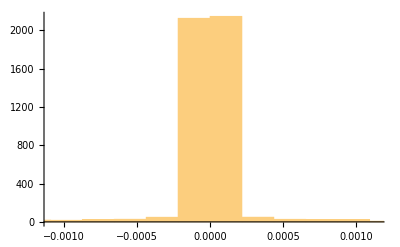

```mathematica
lpsisRGM={};CumStrengthsRGM={};

{EvalsIRGM,EvecsIRGM}=Re[Eigensystem[{He3Ham,He3Norm}]];
EvecGSiRGM=Flatten[EvecsIRGM[[TakeSmallest[EvalsIRGM->"Index",1]]]];
EvalGSiRGM=Min[EvalsIRGM];

Do[

{EvalsFRGM,EvecsFRGM}=Re[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]];
EvecGSfRGM=Flatten[EvecsFRGM[[TakeSmallest[EvalsFRGM->"Index",1]]]];
EvalGSfRGM=Min[EvalsFRGM];

Print["E_0^initial = ",EvalGSiRGM,"    dim(initial) = ",Dimensions[EvalsIRGM]];
Print["E_0^final  = ",EvalGSfRGM,"    dim(final)   = ",Dimensions[EvalsFRGM]];
tmplRGM=0;

Do[
(*inhomoRGM=(Transpose[LitNorm[[nj]]].(CouplingBlockj[[nj]][[mm]][[2]].He3Norm)).EvecGSiRGM;*)
inhomoRGM=CouplingBlockj[[nj]][[mm]][[2]].EvecGSiRGM;
tmplRGM=tmplRGM+(EvecsFRGM.inhomoRGM)^2;
,{mm,Length[mIns[[nj]]]}
];

AppendTo[lpsisRGM,Re[Transpose[{EvalsFRGM,tmplRGM}]]];
AppendTo[CumStrengthsRGM,Re[Transpose[{Sort[lpsisRGM[[nj]]][[All,1]],Accumulate[Sort[lpsisRGM[[nj]]][[All,2]]]}]]];

(*AppendTo[lpsis,Flatten[lpsi,1]];*)

,{nj,Range[1,Length[Subscript[I, n]]]}
]
Histogram[Sort[EvecsFRGM[[1]]]]
```

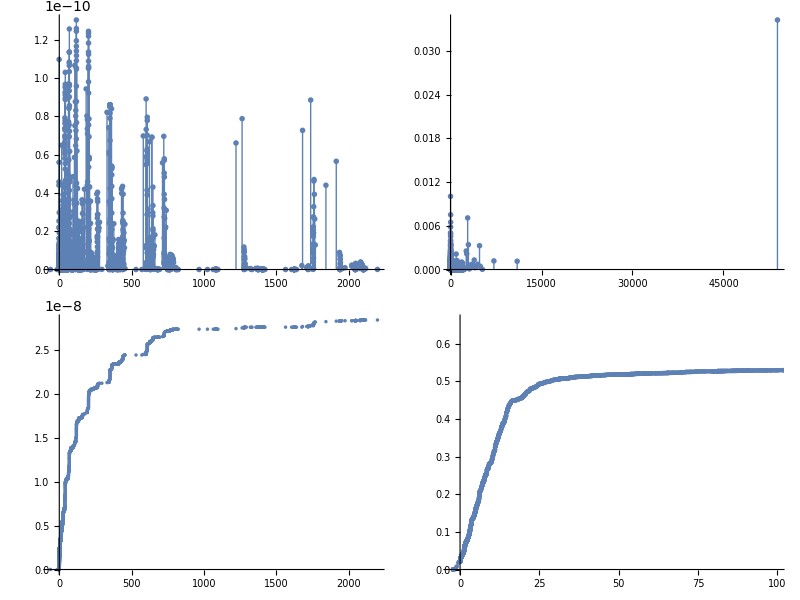

```mathematica
plote3=Grid[{{
ListPlot[Reverse[lpsisRGM[[1]]],Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize],
ListPlot[Reverse[lpsisEV[[1]]],Joined->False,PlotMarkers->{{♔,12},{♗,12}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize]
},{
ListPlot[CumStrengthsRGM,Joined->False,ImageSize->ImgSize,PlotRange->Full,AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{RGM order}",Magnification->2]],
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,100},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]]
}}]
```

#### S(E)=∑_m Ψ_m^2·δ(E-λ_m) → S_benign(E)

C(E):=∫E/0 dΔ S(Δ)=∑_(N_(n,d)) Poly[E,N_numerator]/Poly[E,N_denominator-1]
s.t. C_N/C_M=C(λ_(f,max))  (saturation criterium for equal polynomial orders in numerator and denominator)
F(E)=(∂C)/(∂E)

```mathematica
Put[CumStrengthsEV,LocalObject["CumHelionStrengths_"<>StringTake[resultsDir,{-11,-9}]]]
```

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumHelionStrengths_8f4]

#### Analysis of RHS

```mathematica
(*OμRHSEB=normreg[thresholdLIT,He3Norm];
{λsHeEB,trfHeEB}=Re[Eigensystem[(Transpose[OμRHSEB].He3Ham).OμRHSEB]];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];*)
{λsHe,trfHe}=Re[Eigensystem[{He3Ham,He3Norm}]];
evgs=Flatten[trfHe[[TakeSmallest[λsHe->"Index",1]]]];
inhomo={};

nj=1;mm=1;

tmp=CouplingBlockj[[nj]][[mm]][[2]];

(*OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]]];
{λfinalEB,trfLitEB}=Re[Eigensystem[(Transpose[OμLHSEB].LitHam[[nj]]).OμLHSEB]];
inhomoEB=Transpose[OμLHSEB].((tmp.OμRHSEB).evgsEB);*)

{λfinal,trfLit}=Re[Eigensystem[{LitHam[[nj]],LitNorm[[nj]]}]];
inhomo=tmp.evgs;
```

# of 2-1 states ≥ 219

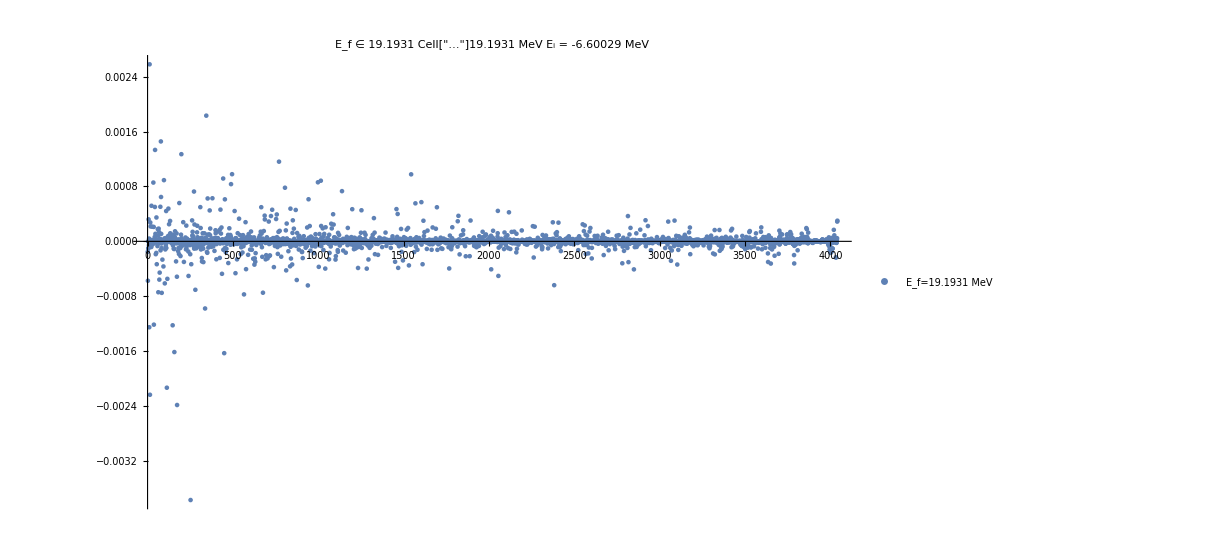
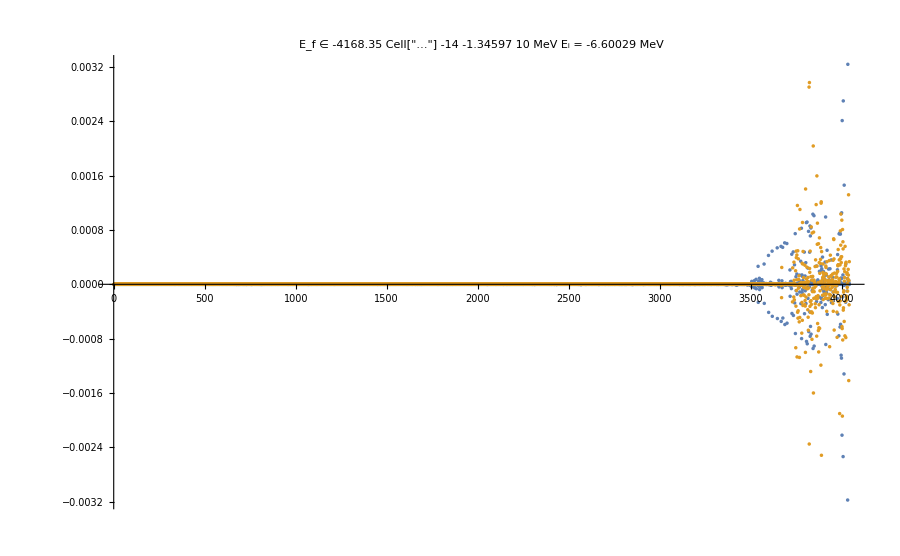
-Graphics- | -Graphics-

-Graphics-1.82662×10^-7  ,  E_f=19.1931 MeV

-Graphics-1.82662×10^-7  ,  E_f=19.1931 MeV

```mathematica
OneTwoConti=Flatten[Position[λfinal,n_/;n<0]];dim21=Length[OneTwoConti];
OrderedSpectF=Join[Delete[λfinal,{#}&/@OneTwoConti],Reverse[λfinal[[OneTwoConti]]]];
OrderedEvecsF=Join[Delete[trfLit,{#}&/@OneTwoConti],Reverse[trfLit[[OneTwoConti]]]];

Print["# of 2-1 states ≥ ",dim21]

nFromTh=2080;
nbrConti=1;
evrng111=Range[-dim21-nbrConti-nFromTh,-dim21-1-nFromTh,20];(*IntegerPart[Subdivide[1,Length[λfinal]-Length[OneTwoConti],20]];*)
evrng21=IntegerPart[Subdivide[1,Length[OneTwoConti],1]];

inhomo111=Re[(inhomo OrderedEvecsF[[#]])&/@evrng111];
inhomo21=Re[(inhomo OrderedEvecsF[[-#]])&/@evrng21];

Grid[{{
ListPlot[inhomo111,AxesLabel->{MaTeX["\\text{RGM basis vector}~m",Magnification->2],MaTeX["c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle",Magnification->2]},ImageSize->ImgSize,PlotRange->Full,PlotLabel->"E_f ∈ "<>ToString[OrderedSpectF[[evrng111[[1]]]]]<>" Cell["…",ExpressionUUID->"9e47a149-332c-40a0-a32a-c438e12a043c"]"<>ToString[OrderedSpectF[[evrng111[[-1]]]]]<>" MeV"<>"      E_i = "<>ToString[TakeSmallest[λsHe,1][[1]]]<>" MeV",PlotLegends->{"E_f="<>ToString[OrderedSpectF[[evrng111[[1]]]]]<>" MeV","E_f="<>ToString[OrderedSpectF[[evrng111[[-1]]]]]<>" MeV"}],
ListPlot[inhomo21,AxesLabel->{MaTeX["\\text{RGM basis vector}~m",Magnification->2],MaTeX["c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle",Magnification->2]},ImageSize->ImgSize,PlotRange->Full,PlotLabel->"E_f ∈ "<>ToString[OrderedSpectF[[-evrng21[[1]]]]]<>" Cell["…",ExpressionUUID->"24da30ac-48b7-40cc-961e-8459b28100a9"]"<>ToString[OrderedSpectF[[-evrng21[[-1]]]]]<>" MeV"<>"      E_i = "<>ToString[TakeSmallest[λsHe,1][[1]]]<>" MeV"]
}}
]
Print[MaTeX["\\left\\vert\\sum_m c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle\\right\\vert^2=",Magnification->1],((Total[#]&/@inhomo111)^2)[[1]],"  ,  E_f=",OrderedSpectF[[evrng111[[1]]]]," MeV"]
Print[MaTeX["\\left\\vert\\sum_m c_m\\cdot\\sum_{n=1}^N c_n~\\left\\langle f_m\\Big\\vert\\widehat{E1}\\Big\\vert i_n\\right\\rangle\\right\\vert^2=",Magnification->1],((Total[#]&/@inhomo111)^2)[[-1]],"  ,  E_f=",OrderedSpectF[[evrng111[[-1]]]]," MeV"]
```